```mathematica
(* Cartesian and Cylindrical FIN DIF   *)


DENS = 1000;
Cp=4200;
k = 0.6;
ALPHA = k/(DENS*Cp);

Delta = 25;
DeltaR = 0.01;
Fo=(ALPHA*Delta)/(DeltaR)^2;

COEFF1=1-2*Fo
(*check for stability *)

To=30;

G=0;

(* 0 cartesian, 1 cylinrical and 2 is spherical *)
```

0.928571

```mathematica
Array [T1,500,0];
Array [T2,500,0];
Array [T3,500,0];
Array [T4,500,0];


T1[0] = 30.;
T2[0] = 30.;
T3[0] = 30.;
T4[0]= 40.;

i = 1;
k=1;

(*  Basic assignment should be ..... 

Ti[k]=(1-Fo*(1+1/(2*i))^G-Fo*(1+1/(2*i))^G)*Ti[k-1]+Fo*(1+1/(2*i))^G*T(i+1)[k-1]+ Fo*(1+1/(2*i))^G*T(i-1)[k-1]

  Now can add PERFUSION,  HEAT GENERATION or CONVECTION   *)

T1[1]=(1-Fo*(1+1/(2*1))^G-Fo*(1-1/(2*1))^G)*T1[0]+Fo*(1+1/(2*1))^G*T2[0]+ Fo*(1-1/(2*k))^G*To;

T2[1]=(1-Fo*(1+1/(2*2))^G-Fo*(1-1/(2*2))^G)*T2[0]+Fo*(1+1/(2*2))^G*T3[0]+ Fo*(1-1/(2*2))^G*T1[0];

T3[1]=(1-Fo*(1+1/(2*3))^G-Fo*(1-1/(2*3))^G)*T3[0]+Fo*(1+1/(2*3))^G*T4[0]+ Fo*(1-1/(2*3))^G*T2[0];

T4[1]=T4[0];

Do[Print [{T1[i], T2[i], T3[i], T4[i]}],{i,1,1}]
```

{30.,30.,30.3571,40.}

```mathematica
Do [T1[i]=(1-Fo*(1+1/(2*1))^G-Fo*(1-1/(2*1))^G)*T1[i-1]+Fo*(1+1/(2*1))^G*T2[i-1]+ Fo*(1-1/(2*1))^G*To,{i,2,200}]

Do[T2[i]=(1-Fo*(1+1/(2*2))^G-Fo*(1-1/(2*2))^G)*T2[i-1]+Fo*(1+1/(2*2))^G*T3[i-1]+ Fo*(1-1/(2*2))^G*T1[i-1],{i,2,200}]

Do[T3[i]=(1-Fo*(1+1/(2*3))^G-Fo*(1-1/(2*3))^G)*T3[i-1]+Fo*(1+1/(2*3))^G*T4[i-1]+ Fo*(1-1/(2*3))^G*T2[i-1],{i,2,200}]

Do[T4[i]=T4[i-1],{i,2,200}];
```

```mathematica
Do[Print [{T1[i*100], T2[i*100], T3[i*100], T4[i*100]}],{i,1,2}]
```

{31.9863,34.2714,36.9833,40.}

{32.4378,34.912,37.4378,40.}

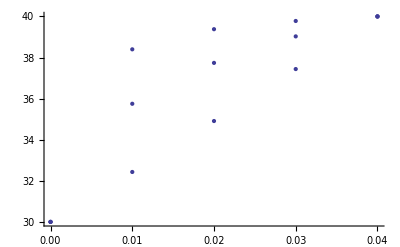

```mathematica
PlotCart=ListPlot [{{0,30},{0.01,32.43},{0.02,34.91},{0.03,37.44},{0.04,40}},PlotStyle->PointSize->Large];
PlotCyl=ListPlot [{{0,30},{0.01,35.75},{0.02,37.74},{0.03,39.03},{0.04,40}},PlotStyle->PointSize->Large];
PlotSph=ListPlot [{{0,30},{0.01,38.4},{0.02,39.38},{0.03,39.78},{0.04,40}},PlotStyle->PointSize->Large];
Show[PlotCart,PlotCyl,PlotSph]
```